# Neural Logic

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
?neurallogic`*
```

## Learn XOR

## Generate training data

```mathematica
numBooleanVariables=10;
Echo[2^numBooleanVariables];
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=200;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->{Soften[Boole[bf@@x]]}]&,Range[maxExamples]];
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

1024

## Create BNN

```mathematica
{softNet,hardNet}=BinaryNN[{NeuralDNFLayer[numBooleanVariables,50,50],NeuralDNFLayer[50,50,50],NeuralDNFLayer[50,50,1]}];
```

```mathematica
bnn=AppendLoss[softNet]
```

NetGraph[<>]

## Train BNN

```mathematica
{trainedBNN,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->testData,
(*LossFunction->"Loss",
BatchSize->16,*)
Method->{"ADAM"},
MaxTrainingRounds->10000];
```

## Evaluate

```mathematica
resultsObject["RoundMeasurements"]
trainedNet=NetExtract[trainedBNN,"NeuralLogicNet"];
```

<|Loss→4.12926×10^-9|>

```mathematica
Log[1]
```

0

### Evaluate soft net

```mathematica
randomTestSample=RandomSample[testData,UpTo[10000]];
softPredictionTargetPairs=[{trainedNet[First[#]],First[Last[#]]}&,randomTestSample];
softPredictionTargetPairs={Harden[#[[1]]],#[[2]]}&/@softPredictionTargetPairs;
Sort[Counts[softPredictionTargetPairs]]
```

<|{{False},0.}→100|>

### Evaluate hard net

```mathematica
trainedBinaryNN=HardBinaryNN[hardNet,trainedNet];
```

```mathematica
hardPredictionTargetPairs=[{First[trainedBinaryNN@@Harden[First[#]]],Harden[First[Last[#]]]}&,randomTestSample];
Sort[Counts[hardPredictionTargetPairs]]
```

<|{False,True}→2,{False,False}→44,{True,True}→54|>

```mathematica
Block[{weights=Flatten[Harden[ExtractWeights[trainedNet]]],bytes,bits},
bytes=Length[weights]/8.0;
bits=StringJoin[ToString/@Boole/@weights];
{bits,Quantity[bytes,"Bytes"],Quantity[bytes/1000.0,"Kilobytes"]}
]
```

{0010010101111011000111110011100100010100100000111001011110100111111000011000010100100001110001011010100000011001011110111101111001001110110001011010000110001101000111001011111000111111001101111001100000010110000011100000001011001111010100101100001110101110101011101110100010001111110100001000001110011001111100111101001100000111101010111100110101010110000010100101110011110100000101100110100010100100000000010011111000010100001111111010011001110100011001111101110001000000101110101100010011101111110000110000001111010111111110110001000100111000111111,68.75 B,0.06875 kB}

```mathematica
trainedBinaryNN;
```

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{0,0,1,0},-Graphics-→{0,1,0,0},-Graphics-→{0,0,1,0},-Graphics-→{0,0,0,1},-Graphics-→{1,0,0,0},-Graphics-→{1,0,0,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,1,0}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Create BNN

```mathematica
f[x_]:=2x-1
g[x_]:=(x+1)/2
```

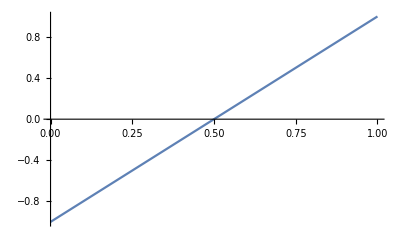

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
Manipulate[Plot[{g[f[x]f[w]]},{x,0,1},PlotRange->{{0,1},{0,1}}],{w,0,1}]
```

```mathematica
g[f[x]f[ w]]//FullSimplify
```

1-x+w (-1+2 x)

```mathematica
{softNet,hardNet}=BinaryNN[{NeuralDNFLayer[Length[First[First[trainData]]],400,20],NeuralMajorityLayer[20,numClasses]}];
```

```mathematica
bnn=AppendLoss[softNet]
```

NetGraph[<>]

```mathematica
NetFlatten[softNet]
```

## Train BNN

```mathematica
{trainedBNN,resultsObject}=NetTrain[bnn,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->RandomSample[testData,UpTo[1000]],
LossFunction->"Loss",
Method->{"ADAM"},
LearningRate->0.01,
MaxTrainingRounds->2000];
```

## Evaluate

```mathematica
trainedNet=NetExtract[trainedBNN,"NeuralLogicNet"]
```

NetChain[<>]

```mathematica
resultsObject["RoundMeasurements"]
```

<|Loss→0.0176878|>

```mathematica
Normal[NetExtract[NetExtract[trainedNet,{1,"AND layer","n2","Weights"}],"Array"]]
```

{0.398132,0.606753,0.539664,0.585166,0.362243,0.106043,-0.222237,0.394982,0.567335,0.851364,0.344152,-0.102666,-0.226496,-0.131803,0.0146996,0.645838,0.260452,0.285985,-0.140932,0.849262,-0.0332097,-0.0468388,-0.0594959,0.0622434,0.127709,0.00546322,-0.0670407,-0.250543,0.488968,0.880685,-0.155249,0.789476,0.124988,-0.224938,-0.0376439,-0.0514525,0.869083,-0.041351,-0.248035,0.77163,0.40442,-0.256865,-0.0965249,-0.189232,-0.221002,0.89016,-0.137812,0.747146,0.093758,0.776528,-0.288912,0.174973,-0.092932,-0.0650848,0.0784919,0.716633,0.76331,0.710689,0.297747,0.33658,0.0916135,0.352193,0.608589,0.499241}

### Evaluate soft net

```mathematica
randomTestSample=RandomSample[testData,UpTo[2000]];
softPredictionTargetPairs=[{trainedNet[First[#]],Last[#]}&,randomTestSample];
softPredictionTargetPairs={Harden[#[[1]]],#[[2]]}&/@softPredictionTargetPairs;
Reverse[Sort[Counts[softPredictionTargetPairs]]]
```

<|{{False,True},{0,1}}→1053,{{True,False},{1,0}}→901,{{True,True},{0,1}}→35,{{False,True},{1,0}}→6,{{True,False},{0,1}}→4,{{True,True},{1,0}}→1|>

```mathematica
nal=NeuralAND[{0.75,0.75,0.75,0.75}]
```

NetGraph[<>]

```mathematica
nal[{0.25,0.5,0.5,0.5}]
```

{0.106812}

### Evaluate hard net

```mathematica
trainedBinaryNN=HardBinaryNN[hardNet,trainedNet];
```

```mathematica
hardPredictionTargetPairs=[{trainedBinaryNN@@Harden[First[#]],Harden[Last[#]]}&,randomTestSample];
Sort[Counts[hardPredictionTargetPairs]]
```

<|{{True,True,False,False},{True,False,False,False}}→1,{{False,True,True,False},{False,False,False,True}}→1,{{False,True,False,False},{True,False,False,False}}→1,{{False,False,True,True},{True,False,False,False}}→1,{{False,True,False,True},{False,False,True,False}}→1,{{True,False,True,True},{True,False,False,False}}→2,{{True,False,True,False},{False,False,False,True}}→2,{{False,True,False,True},{True,False,False,False}}→2,{{False,False,True,False},{False,True,False,False}}→3,{{True,False,False,False},{False,False,False,True}}→7,{{False,False,True,False},{True,False,False,False}}→7,{{False,True,True,False},{False,True,False,False}}→7,{{True,False,False,False},{False,False,True,False}}→8,{{False,False,False,True},{False,True,False,False}}→8,{{True,False,False,True},{False,False,False,True}}→9,{{False,True,False,True},{False,False,False,True}}→15,{{False,False,True,True},{False,False,False,True}}→17,{{False,False,True,False},{False,False,False,True}}→18,{{True,False,True,False},{False,False,True,False}}→19,{{False,True,True,False},{False,False,True,False}}→20,{{False,False,False,True},{False,False,True,False}}→20,{{False,True,False,False},{False,False,False,True}}→21,{{False,False,True,True},{False,False,True,False}}→23,{{True,False,False,True},{True,False,False,False}}→23,{{False,False,False,True},{True,False,False,False}}→23,{{True,False,True,False},{True,False,False,False}}→24,{{False,True,False,False},{False,False,True,False}}→29,{{False,True,False,True},{False,True,False,False}}→33,{{False,False,False,False},{False,True,False,False}}→54,{{False,False,False,False},{True,False,False,False}}→55,{{False,False,False,False},{False,False,False,True}}→108,{{False,False,False,False},{False,False,True,False}}→111,{{False,False,True,False},{False,False,True,False}}→257,{{False,False,False,True},{False,False,False,True}}→289,{{True,False,False,False},{True,False,False,False}}→354,{{False,True,False,False},{False,True,False,False}}→427|>

```mathematica
Block[{weights=Flatten[Harden[ExtractWeights[trainedNet]]],bytes,bits},
bytes=Length[weights]/8.0;
bits=StringJoin[ToString/@Boole/@weights];
{Iconize[bits],Quantity[bytes,"Bytes"],Quantity[bytes/1000.0,"Kilobytes"]}
]
```

{,2550. B,2.55 kB}

```mathematica
trainedBinaryNN;
```

## Notes

```mathematica
Manipulate[Plot[{1/2(w+b),0.5},{b,0,1},PlotRange->{{0,1},{0,1}}],{w,0,1}]
```

```mathematica
SquashTo01[x_]:=x/(x+ⅇ^-x)
```

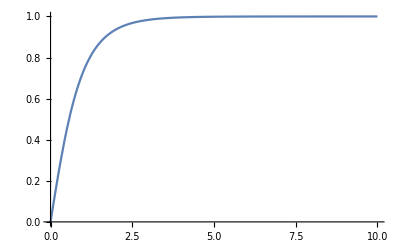

```mathematica
Plot[SquashTo01[x],{x,0,10},PlotRange->All]
```

```mathematica
Solve[SquashTo01[x]==y,x]
```

{{x→ProductLog[-y/(-1+y)]}}

```mathematica
Explode[x_]:=ProductLog[-x/(x-1)]
```

```mathematica
Explode[1]
```

∞

```mathematica
Explode[0.999]
```

5.24876

```mathematica
Explode[1/2]//N
```

0.567143

```mathematica
Explode[0]
```

0

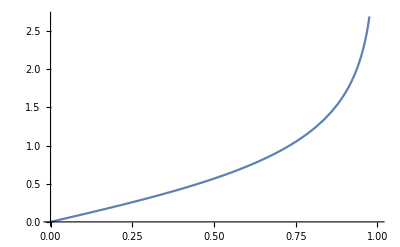

```mathematica
Plot[Explode[x],{x,0,1}]
```

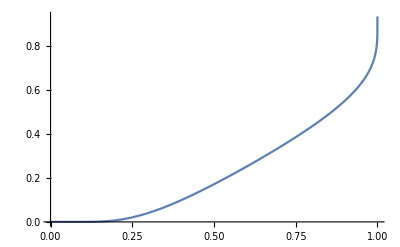

```mathematica
Plot[ⅇ^(-1/(Explode[x])),{x,0,1},PlotRange->All]
```

```mathematica
Manipulate[Plot[ⅇ^(-1/(Explode[x])),{x,0,1},PlotRange->{{0,1},{0,1}}],{w,0,1}]
```